```mathematica
ClearAll["Global`*"];
```

```mathematica
ℰ=10^(-3);znak=3;

X0={-1,-2};α=1000; f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2

(*X0={0,√10};f[{x_,y_}]:=10 x^2+7 y^2-4x y-4 √5(5x-y)-16;*) (*X0={0,-√5};X0={0,√10};*)

uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]
X=X0;
points={X0};
fValues={f[X0]};

Subscript[α, 1]=1;Subscript[α, 2]=1;
Subscript[e, 1]={1,0};Subscript[e, 2]={0,1};

β=1;u=Subscript[α, 1] Subscript[e, 1]+Subscript[α, 2] Subscript[e, 2];
basis=0;

i=0;

While[True,(*Метод циклического покоординатного спуска*)
Subscript[α, 1]=NArgMin[f[X+κ Subscript[e, 1]],κ,StepMonitor:>i++];
X+=Subscript[α, 1] Subscript[e, 1]; 
 Subscript[α, 2]=NArgMin[f[X+κ Subscript[e, 2]],κ,StepMonitor:>i++];
X+=Subscript[α, 2] Subscript[e, 2]; 

(*Метод Хука-Дживса*)
(*u=Subscript[α, 1] Subscript[e, 1]+Subscript[α, 2] Subscript[e, 2];β=NArgMin[f[X+κ u],κ,StepMonitor:>i++];X+=β u;*)

(*Метод Розенброка*)
(*Subscript[e, 1]=Subscript[α, 1] Subscript[e, 1]+Subscript[α, 2] Subscript[e, 2];{Subscript[e, 1],Subscript[e, 2]}=Orthogonalize[{Subscript[e, 1],Subscript[e, 2]}];*)

(*Метод Пауэлла*)
u=Subscript[α, 1] Subscript[e, 1]+Subscript[α, 2] Subscript[e, 2];basis++;
β=NArgMin[f[X+κ u],κ,StepMonitor:>i++];
X+=β u;

Subscript[e, 1]=Subscript[e, 2];
Subscript[e, 2]=u;
If[basis≠2,Continue[];];basis=0;

 points=Append[points,X];
fValues=Append[fValues,f[X]];   i++;
If[(Norm[points[[-1]]-points[[-2]]]<ℰ )&& (Norm[fValues[[-1]]-fValues[[-2]]]<ℰ),Break[];];
];"Результат получен за "<>ToString[Length[points]-1]<> " итерации."
"Точка минимума X^* = "
SetAccuracy[X,znak]
"Минимальное значение функции: f(X^*) = "
SetAccuracy[f[X],znak]
"Количество обращений к функции : i = "
i
```

Результат получен за 8 итерации.

Точка минимума X^* =

{1.,1.}

Минимальное значение функции: f(X^*) =

0.

Количество обращений к функции : i =

3374

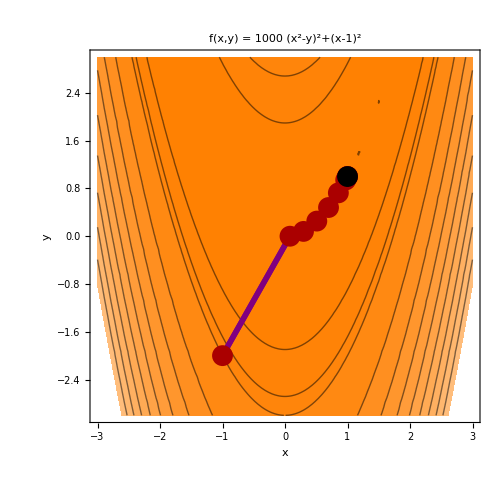

```mathematica
a=2; b=3;с=2; CP0={-3,-3}; CP1={3,3};
(*a=1; b=1; c=1; CP0={-2,-2}; CP1={4,4}; (*квадратичная, Паул*)
a=4; b=5; c=4; CP0={-2,-2}; CP1={4,4}; (*Квадратичная ,остальные*)*)

(*a=2; b=3; c=2; CP0={-3,-3}; CP1={3,3}; (*Розенброк при 1,50,1000*)*)
 a:=Length[points]-1;b:=Length[points];
ContourPlot[f[{x,y}],{x,CP0[[1]],CP1[[1]]},{y,CP0[[2]],CP1[[2]]},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;2]]~Join~{fValues[[a]],fValues[[b]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large](*,LabelStyle->Large*),FrameStyle->Thick,ImageSize->500,Epilog->{Purple,Thickness[0.008],Line[points],Table[Arrow[points[[i-1;;i]]],{i,2,c}],Darker[Red],PointSize[0.03],Point[points],Black,Point[points[[Length[points]]]]}]
```